Metricas del fluido perfecto e Indice politropo

```mathematica
ξ[r_]:=Log[B^2(1+r^2/A^2)]; μ[r_]:=-Log[((1-r^2/c^2)(1+r^2/A^2))/(1+(2 r^2)/A^2)];Γ:=1+1/n
```

Ecuacion diferencial master

```mathematica
DSolve[f'[r]/r+f[r]/r^2==-(κ Ka)^((Γ-1)/Γ)(Exp[-μ[r]](1/r^2+ξ'[r]/r)-1/r^2)^(1/Γ),f[r],r]
```

{{f[r]→-1/3 r^2 ((-A^2+c^2-3 r^2)/(c^2 (A^2+2 r^2)))^(n/(1+n)) ((A^2-c^2+3 r^2)/(A^2-c^2))^(-n/(1+n)) (1+(2 r^2)/A^2)^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-n/(1+n),n/(1+n),5/2,(3 r^2)/(-A^2+c^2),-(2 r^2)/A^2]+C[1]/r}}

```mathematica
f[r_]:=-1/3 r^2 ((-A^2+c^2-3 r^2)/(c^2 (A^2+2 r^2)))^(n/(1+n)) ((A^2-c^2+3 r^2)/(A^2-c^2))^(-n/(1+n)) (1+(2 r^2)/A^2)^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-n/(1+n),n/(1+n),5/2,(3 r^2)/(-A^2+c^2),-(2 r^2)/A^2]+c1/r
```

```mathematica
f[r]//FullSimplify
```

c1/r-1/3 r^2 ((-A^2+c^2-3 r^2)/(c^2 (A^2+2 r^2)))^(n/(1+n)) (1+(2 r^2)/A^2)^(n/(1+n)) (1+(3 r^2)/(A^2-c^2))^(-1+1/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,(3 r^2)/(-A^2+c^2),-(2 r^2)/A^2]

```mathematica
f[r_]:=c1/r-1/3 r^2 ((-A^2+c^2-3 r^2)/(c^2 (A^2+2 r^2)))^(n/(1+n)) (1+(2 r^2)/A^2)^(n/(1+n)) (1+(3 r^2)/(A^2-c^2))^(-1+1/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,(3 r^2)/(-A^2+c^2),-(2 r^2)/A^2]
```

```mathematica
c1:=0
```

```mathematica
f[r]//FullSimplify
```

-1/3 r^2 ((-A^2+c^2-3 r^2)/(c^2 (A^2+2 r^2)))^(n/(1+n)) (1+(2 r^2)/A^2)^(n/(1+n)) (1+(3 r^2)/(A^2-c^2))^(-1+1/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,(3 r^2)/(-A^2+c^2),-(2 r^2)/A^2]

```mathematica
((-A^2+c^2-3 r^2)/(c^2 (A^2+2 r^2)))(1+(2 r^2)/A^2)(1/(1+(3 r^2)/(A^2-c^2)))//FullSimplify
```

1/A^2-1/c^2

```mathematica
f[r_]:=-1/3 r^2 ((c^2-A^2)/(A^2 c^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,(3 r^2)/(-A^2+c^2),-(2 r^2)/A^2]
```

```mathematica
f[r]//FullSimplify
```

-1/3 (1/A^2-1/c^2)^(n/(1+n)) r^2 (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,(3 r^2)/(-A^2+c^2),-(2 r^2)/A^2]

Derivada de la otra funcion de deformacion

```mathematica
gprime[r_]:=(1/(Exp[-μ[r]]+f[r]))((Ka^Γ Exp[-μ[r]]-f[r])(ξ'[r]+1/r)-Ka^Γ/r)
```

```mathematica
gprime[r]//FullSimplify
```

(r (3 Ka^(1+1/n) (A^2+r^2) (A^2-c^2+3 r^2)-(1/A^2-1/c^2)^(n/(1+n)) c^2 (A^4+5 A^2 r^2+6 r^4) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,(3 r^2)/(-A^2+c^2),-(2 r^2)/A^2]))/((A^2+r^2) (3 (-c+r) (c+r) (A^2+r^2)+(1/A^2-1/c^2)^(n/(1+n)) c^2 r^2 (A^2+2 r^2) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,(3 r^2)/(-A^2+c^2),-(2 r^2)/A^2]))

```mathematica
gprime[r_]:=(r (3 Ka^(1+1/n) (A^2+r^2) (A^2-c^2+3 r^2)-(1/A^2-1/c^2)^(n/(1+n)) c^2 (A^4+5 A^2 r^2+6 r^4) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,(3 r^2)/(-A^2+c^2),-(2 r^2)/A^2]))/((A^2+r^2) (3 (-c+r) (c+r) (A^2+r^2)+(1/A^2-1/c^2)^(n/(1+n)) c^2 r^2 (A^2+2 r^2) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,(3 r^2)/(-A^2+c^2),-(2 r^2)/A^2]))
```

presion del fluido perfecto

```mathematica
pr[r_]:=(-A^2+c^2-3 r^2)/(c^2 (A^2+2 r^2) κ)
```

Aplicando la condicion de matching en la superficie en cuanto a la presion

```mathematica
pr[R]+f[R]/κ(1/R^2+(ξ'[R]+gprime[R])/R)+gprime[R]/(κ R)Exp[-μ[R]]//FullSimplify
```

((1+Ka^(1+1/n)) (-A^2+c^2-3 R^2))/(c^2 (A^2+2 R^2) κ)

```mathematica
Solve[((1+Ka^(1+1/n)) (-A^2+c^2-3 R^2))/(c^2 (A^2+2 R^2) κ)==0,c]
```

{{c→-√(A^2+3 R^2)},{c→√(A^2+3 R^2)}}

```mathematica
c:=√(A^2+3 R^2)
```

```mathematica
f[r]//FullSimplify
```

-3^(-1/(1+n)) r^2 (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2]

```mathematica
Exp[-μ[R]]//FullSimplify
```

(A^2+R^2)/(A^2+3 R^2)

La presión radial efectiva

```mathematica
Pr[r_]:=(1+Ka^Γ )pr[r]
```

```mathematica
Pr[r]//FullSimplify
```

-(3 (1+Ka^(1+1/n)) (r-R) (r+R))/((A^2+2 r^2) (A^2+3 R^2) κ)

```mathematica
Pr[r_]:=-(3 (1+Ka^(1+1/n)) (r-R) (r+R))/((A^2+2 r^2) (A^2+3 R^2) κ)
```

Densidad del fluido perfecto

```mathematica
ρ[r_]:=(3 A^2 (A^2+c^2)+(7 A^2+2 c^2) r^2+6 r^4)/(c^2 (A^2+2 r^2)^2 κ)
```

Densidad del polítropo

```mathematica
densitypoly[r_]:=-1/κ(f[r]/r^2+f'[r]/r)
```

```mathematica
densitypoly[r]//FullSimplify
```

(3^(n/(1+n)) (1+(2 r^2)/A^2)^(-1+1/(1+n)) (1-r^2/R^2)^(-1/(1+n)) (-r^2+R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)))/(R^2 κ)

```mathematica
(1/(1+(2 r^2)/A^2))(R^2/(A^4+3 A^2 R^2)) //FullSimplify
```

R^2/((A^2+2 r^2) (A^2+3 R^2))

```mathematica
densitypoly[r_]:= (3^(n/(1+n))  (1-r^2/R^2)^(-1/(1+n)) (-r^2+R^2) (R^2/((A^2+2 r^2) (A^2+3 R^2)))^(n/(1+n)) (Ka κ)^(1/(1+n)))/(R^2 κ)
```

Densidad efectiva

```mathematica
RO[r_]:=ρ[r]+densitypoly[r]
```

```mathematica
RO[r]//FullSimplify
```

1/κ((6 A^4+9 A^2 (r^2+R^2)+6 r^2 (r^2+R^2))/((A^2+2 r^2)^2 (A^2+3 R^2))+(3^(n/(1+n)) (1-r^2/R^2)^(-1/(1+n)) (-r+R) (r+R) (R^2/((A^2+2 r^2) (A^2+3 R^2)))^(n/(1+n)) (Ka κ)^(1/(1+n)))/R^2)

```mathematica
RO[r_]:=1/κ((6 A^4+9 A^2 (r^2+R^2)+6 r^2 (r^2+R^2))/((A^2+2 r^2)^2 (A^2+3 R^2))+(3^(n/(1+n)) (1-r^2/R^2)^(-1/(1+n)) (-r+R) (r+R) (R^2/((A^2+2 r^2) (A^2+3 R^2)))^(n/(1+n)) (Ka κ)^(1/(1+n)))/R^2)
```

```mathematica
Z2[r_]:=Exp[-μ[r]]/4(2D[gprime[r],r]+(gprime[r])^2+(2gprime[r])/r+2ξ'[r]* gprime[r]-μ'[r]*gprime[r])
```

```mathematica
Z2[r]//FullSimplify
```

(A^2 (1+r^2/A^2) (1-r^2/(A^2+3 R^2)) (81 Ka^(2+2/n) r^2 (A^2+r^2) (A^2+2 r^2) R^2 (r^2-R^2)^2 (A^2-r^2+3 R^2)-108 Ka^(1+1/n) r^2 (A^2+r^2)^2 (A^2+2 r^2) R^2 (A^2-r^2+3 R^2)^2-108 Ka^(1+1/n) (A^2+r^2)^2 (A^2+2 r^2) (r-R) R^2 (r+R) (A^2-r^2+3 R^2)^2+54 Ka^(1+1/n) r^2 (A^2+r^2) (r-R) R^2 (r+R) (A^2-r^2+3 R^2) (2 (A^4+A^2 r^2+r^4)+3 A^2 R^2)+54 Ka^(1+1/n) r (A^2+r^2)^2 (A^2+2 r^2) (r-R) R^2 (r+R) (-A^2+r^2-3 R^2) (r-√(A^2+3 R^2))+54 Ka^(1+1/n) r (A^2+r^2)^2 (A^2+2 r^2) (r-R) R^2 (r+R) (-A^2+r^2-3 R^2) (r+√(A^2+3 R^2))+2 3^(1+n/(1+n)) (A^2+2 r^2) R^2 (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (2 A^10+4 A^8 (4 r^2+3 R^2)+3 A^6 ((4+Ka^(1+1/n)) r^4+(35+Ka^(1+1/n)) r^2 R^2+6 R^4)+6 r^6 (3 r^4-(21+5 Ka^(1+1/n)) r^2 R^2+9 (4+Ka^(1+1/n)) R^4)+A^4 r^2 (-38 r^4+162 r^2 R^2+171 R^4-3 Ka^(1+1/n) (r^2-3 R^2) (4 r^2+R^2))+A^2 r^4 (-10 r^4-81 r^2 R^2+387 R^4-3 Ka^(1+1/n) (3 r^4+5 r^2 R^2-24 R^4))) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2]+r^2 (A^2+2 r^2)^2 R^2 (A^2+3 R^2)^2 (A^6-2 A^4 r^2+7 A^2 r^4+18 r^6+3 A^4 R^2-9 A^2 r^2 R^2-18 r^4 R^2) (1/A^2-1/(A^2+3 R^2))^((2 n)/(1+n)) (Ka κ)^(2/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2]^2-2 3^(2+n/(1+n)) A^2 (A^2+r^2) (A^2+2 r^2) (1+(2 r^2)/A^2)^(1/(1+n)) (1-r^2/R^2)^(-1/(1+n)) (A^2+3 R^2) (A^2-r^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (-3 Ka^(1+1/n) r^2 (r-R) (r+R)+(A^2+3 r^2) (A^2-r^2+3 R^2)) (Ka κ)^(1/(1+n)) (r^2-R^2+(1+(2 r^2)/A^2)^(n/(1+n)) (1-r^2/R^2)^(1/(1+n)) R^2 AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2])))/(4 (A^2+2 r^2)^2 R^2 (A^4-r^4+3 (A^2+r^2) R^2) (-3 (A^2+r^2) (A^2-r^2+3 R^2)+r^2 (A^2+2 r^2) (A^2+3 R^2) (1/A^2-1/(A^2+3 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2])^2)

```mathematica
Z2[r_]:=(A^2 (1+r^2/A^2) (1-r^2/(A^2+3 R^2)) (81 Ka^(2+2/n) r^2 (A^2+r^2) (A^2+2 r^2) R^2 (r^2-R^2)^2 (A^2-r^2+3 R^2)-108 Ka^(1+1/n) r^2 (A^2+r^2)^2 (A^2+2 r^2) R^2 (A^2-r^2+3 R^2)^2-108 Ka^(1+1/n) (A^2+r^2)^2 (A^2+2 r^2) (r-R) R^2 (r+R) (A^2-r^2+3 R^2)^2+54 Ka^(1+1/n) r^2 (A^2+r^2) (r-R) R^2 (r+R) (A^2-r^2+3 R^2) (2 (A^4+A^2 r^2+r^4)+3 A^2 R^2)+54 Ka^(1+1/n) r (A^2+r^2)^2 (A^2+2 r^2) (r-R) R^2 (r+R) (-A^2+r^2-3 R^2) (r-√(A^2+3 R^2))+54 Ka^(1+1/n) r (A^2+r^2)^2 (A^2+2 r^2) (r-R) R^2 (r+R) (-A^2+r^2-3 R^2) (r+√(A^2+3 R^2))+2 3^(1+n/(1+n)) (A^2+2 r^2) R^2 (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (2 A^10+4 A^8 (4 r^2+3 R^2)+3 A^6 ((4+Ka^(1+1/n)) r^4+(35+Ka^(1+1/n)) r^2 R^2+6 R^4)+6 r^6 (3 r^4-(21+5 Ka^(1+1/n)) r^2 R^2+9 (4+Ka^(1+1/n)) R^4)+A^4 r^2 (-38 r^4+162 r^2 R^2+171 R^4-3 Ka^(1+1/n) (r^2-3 R^2) (4 r^2+R^2))+A^2 r^4 (-10 r^4-81 r^2 R^2+387 R^4-3 Ka^(1+1/n) (3 r^4+5 r^2 R^2-24 R^4))) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2]+r^2 (A^2+2 r^2)^2 R^2 (A^2+3 R^2)^2 (A^6-2 A^4 r^2+7 A^2 r^4+18 r^6+3 A^4 R^2-9 A^2 r^2 R^2-18 r^4 R^2) (1/A^2-1/(A^2+3 R^2))^((2 n)/(1+n)) (Ka κ)^(2/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2]^2-2 3^(2+n/(1+n)) A^2 (A^2+r^2) (A^2+2 r^2) (1+(2 r^2)/A^2)^(1/(1+n)) (1-r^2/R^2)^(-1/(1+n)) (A^2+3 R^2) (A^2-r^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (-3 Ka^(1+1/n) r^2 (r-R) (r+R)+(A^2+3 r^2) (A^2-r^2+3 R^2)) (Ka κ)^(1/(1+n)) (r^2-R^2+(1+(2 r^2)/A^2)^(n/(1+n)) (1-r^2/R^2)^(1/(1+n)) R^2 AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2])))/(4 (A^2+2 r^2)^2 R^2 (A^4-r^4+3 (A^2+r^2) R^2) (-3 (A^2+r^2) (A^2-r^2+3 R^2)+r^2 (A^2+2 r^2) (A^2+3 R^2) (1/A^2-1/(A^2+3 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2])^2)
```

La derivada de la componente métrica temporal efectiva

```mathematica
nuprime[r_]:=ξ'[r]+gprime[r]
```

La presión tangencial del polítropo

```mathematica
PT[r_]:=1/κ(f[r]/4(2nuprime'[r]+(nuprime[r])^2+(2nuprime[r])/r )-f'[r]/4(nuprime[r]+2/r)+Z2[r])
```

```mathematica
PT[r]//FullSimplify
```

1/(12 (A^2+2 r^2)^2 κ)(1-r^2/R^2)^(-1/(1+n)) (-((27 (A^2+r^2) (A^2-r^2+3 R^2) (24 A^6 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^2+48 A^4 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^2-9 A^2 Ka^(2+2/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^2-36 Ka^(1+1/n) r^8 (1-r^2/R^2)^(1/(1+n)) R^2-18 Ka^(2+2/n) r^8 (1-r^2/R^2)^(1/(1+n)) R^2-12 A^6 Ka^(1+1/n) (1-r^2/R^2)^(1/(1+n)) R^4+48 A^4 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^4+186 A^2 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^4+18 A^2 Ka^(2+2/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^4+156 Ka^(1+1/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^4+36 Ka^(2+2/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^4-36 A^4 Ka^(1+1/n) (1-r^2/R^2)^(1/(1+n)) R^6-90 A^2 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^6-9 A^2 Ka^(2+2/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^6-72 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^6-18 Ka^(2+2/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^6+2 3^(n/(1+n)) A^2 (A^2+2 r^2) (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (-3 Ka^(1+1/n) r^2 (r-R) (r+R)+(A^2+3 r^2) (A^2-r^2+3 R^2)) (Ka κ)^(1/(1+n))))/(R^2 (A^2+3 R^2) (-3 (A^2+r^2) (A^2-r^2+3 R^2)+r^2 (A^2+2 r^2) (A^2+3 R^2) (1/A^2-1/(A^2+3 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2])^2))+(3^(n/(1+n)) (A^2+2 r^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) (-27 A^2 (A^2+r^2) (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (A^2-r^2+3 R^2) (-3 Ka^(1+1/n) r^2 (r-R) (r+R)+2 (A^2+2 r^2) (A^2-r^2+3 R^2))-AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2] (9 (2 r^6 (1-r^2/R^2)^(1/(1+n)) R^2 (8 r^4-30 r^2 R^2+18 R^4+9 Ka^(2+2/n) (r^2-R^2)^2+3 Ka^(1+1/n) (11 r^4-42 r^2 R^2+15 R^4))+A^10 (4 (1-r^2/R^2)^(1/(1+n)) R^2-5 3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)))+A^6 ((1-r^2/R^2)^(1/(1+n)) R^2 (-((22+51 Ka^(1+1/n)) r^4)+3 (22+9 Ka^(1+1/n)) r^2 R^2+36 R^4)+3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) ((-1+9 Ka^(1+1/n)) r^4-3 (37+3 Ka^(1+1/n)) r^2 R^2-45 R^4) (Ka κ)^(1/(1+n)))+2 A^8 (3 (1-r^2/R^2)^(1/(1+n)) R^2 (r^2+4 R^2)-3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (8 r^4+7 r^2 R^2-15 R^4) (Ka κ)^(1/(1+n)))+3 A^2 r^4 R^2 ((1-r^2/R^2)^(1/(1+n)) (6 r^4-46 r^2 R^2+48 R^4+3 Ka^(2+2/n) (r^2-R^2)^2+Ka^(1+1/n) (9 r^4-124 r^2 R^2+51 R^4))+2 3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (9 Ka^(1+1/n) (r-R) (r+R)+11 (r^2-3 R^2)) (Ka κ)^(1/(1+n)))+A^4 r^2 ((1-r^2/R^2)^(1/(1+n)) R^2 (-22 r^4-36 r^2 R^2+144 R^4-3 Ka^(1+1/n) (26 r^4+41 r^2 R^2-27 R^4))+3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (22 r^4-69 r^2 R^2-189 R^4+9 Ka^(1+1/n) (2 r^4+r^2 R^2-3 R^4)) (Ka κ)^(1/(1+n))))+r^2 (A^2+2 r^2) (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2] (3^(1+n/(1+n)) ((1-r^2/R^2)^(1/(1+n)) R^2 (-6 A^6-10 A^4 r^2+20 A^2 r^4+20 r^6-6 (3 A^4+9 A^2 r^2+4 r^4) R^2+3 Ka^(1+1/n) r^2 (10 r^4-2 r^2 R^2+A^2 (9 r^2-5 R^2)))+3^(n/(1+n)) A^2 r^2 (A^2+2 r^2) (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)))+2 9^(n/(1+n)) r^2 (A^2+2 r^2)^2 (1-r^2/R^2)^(1/(1+n)) R^2 (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2]))))/(-3 (A^2+r^2) R (A^2-r^2+3 R^2)+r^2 (A^2+2 r^2) R (A^2+3 R^2) (1/A^2-1/(A^2+3 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2])^2)

```mathematica
PT[r_]=1/(12 (A^2+2 r^2)^2 κ)(1-r^2/R^2)^(-1/(1+n)) (-((27 (A^2+r^2) (A^2-r^2+3 R^2) (24 A^6 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^2+48 A^4 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^2-9 A^2 Ka^(2+2/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^2-36 Ka^(1+1/n) r^8 (1-r^2/R^2)^(1/(1+n)) R^2-18 Ka^(2+2/n) r^8 (1-r^2/R^2)^(1/(1+n)) R^2-12 A^6 Ka^(1+1/n) (1-r^2/R^2)^(1/(1+n)) R^4+48 A^4 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^4+186 A^2 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^4+18 A^2 Ka^(2+2/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^4+156 Ka^(1+1/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^4+36 Ka^(2+2/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^4-36 A^4 Ka^(1+1/n) (1-r^2/R^2)^(1/(1+n)) R^6-90 A^2 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^6-9 A^2 Ka^(2+2/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^6-72 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^6-18 Ka^(2+2/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^6+2 3^(n/(1+n)) A^2 (A^2+2 r^2) (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (-3 Ka^(1+1/n) r^2 (r-R) (r+R)+(A^2+3 r^2) (A^2-r^2+3 R^2)) (Ka κ)^(1/(1+n))))/(R^2 (A^2+3 R^2) (-3 (A^2+r^2) (A^2-r^2+3 R^2)+r^2 (A^2+2 r^2) (A^2+3 R^2) (1/A^2-1/(A^2+3 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2])^2))+(3^(n/(1+n)) (A^2+2 r^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) (-27 A^2 (A^2+r^2) (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (A^2-r^2+3 R^2) (-3 Ka^(1+1/n) r^2 (r-R) (r+R)+2 (A^2+2 r^2) (A^2-r^2+3 R^2))-AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2] (9 (2 r^6 (1-r^2/R^2)^(1/(1+n)) R^2 (8 r^4-30 r^2 R^2+18 R^4+9 Ka^(2+2/n) (r^2-R^2)^2+3 Ka^(1+1/n) (11 r^4-42 r^2 R^2+15 R^4))+A^10 (4 (1-r^2/R^2)^(1/(1+n)) R^2-5 3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)))+A^6 ((1-r^2/R^2)^(1/(1+n)) R^2 (-((22+51 Ka^(1+1/n)) r^4)+3 (22+9 Ka^(1+1/n)) r^2 R^2+36 R^4)+3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) ((-1+9 Ka^(1+1/n)) r^4-3 (37+3 Ka^(1+1/n)) r^2 R^2-45 R^4) (Ka κ)^(1/(1+n)))+2 A^8 (3 (1-r^2/R^2)^(1/(1+n)) R^2 (r^2+4 R^2)-3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (8 r^4+7 r^2 R^2-15 R^4) (Ka κ)^(1/(1+n)))+3 A^2 r^4 R^2 ((1-r^2/R^2)^(1/(1+n)) (6 r^4-46 r^2 R^2+48 R^4+3 Ka^(2+2/n) (r^2-R^2)^2+Ka^(1+1/n) (9 r^4-124 r^2 R^2+51 R^4))+2 3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (9 Ka^(1+1/n) (r-R) (r+R)+11 (r^2-3 R^2)) (Ka κ)^(1/(1+n)))+A^4 r^2 ((1-r^2/R^2)^(1/(1+n)) R^2 (-22 r^4-36 r^2 R^2+144 R^4-3 Ka^(1+1/n) (26 r^4+41 r^2 R^2-27 R^4))+3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (22 r^4-69 r^2 R^2-189 R^4+9 Ka^(1+1/n) (2 r^4+r^2 R^2-3 R^4)) (Ka κ)^(1/(1+n))))+r^2 (A^2+2 r^2) (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2] (3^(1+n/(1+n)) ((1-r^2/R^2)^(1/(1+n)) R^2 (-6 A^6-10 A^4 r^2+20 A^2 r^4+20 r^6-6 (3 A^4+9 A^2 r^2+4 r^4) R^2+3 Ka^(1+1/n) r^2 (10 r^4-2 r^2 R^2+A^2 (9 r^2-5 R^2)))+3^(n/(1+n)) A^2 r^2 (A^2+2 r^2) (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)))+2 9^(n/(1+n)) r^2 (A^2+2 r^2)^2 (1-r^2/R^2)^(1/(1+n)) R^2 (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2]))))/(-3 (A^2+r^2) R (A^2-r^2+3 R^2)+r^2 (A^2+2 r^2) R (A^2+3 R^2) (1/A^2-1/(A^2+3 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2])^2)
```

1/(12 (A^2+2 r^2)^2 κ)(1-r^2/R^2)^(-1/(1+n)) (-((27 (A^2+r^2) (A^2-r^2+3 R^2) (24 A^6 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^2+48 A^4 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^2-9 A^2 Ka^(2+2/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^2-36 Ka^(1+1/n) r^8 (1-r^2/R^2)^(1/(1+n)) R^2-18 Ka^(2+2/n) r^8 (1-r^2/R^2)^(1/(1+n)) R^2-12 A^6 Ka^(1+1/n) (1-r^2/R^2)^(1/(1+n)) R^4+48 A^4 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^4+186 A^2 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^4+18 A^2 Ka^(2+2/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^4+156 Ka^(1+1/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^4+36 Ka^(2+2/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^4-36 A^4 Ka^(1+1/n) (1-r^2/R^2)^(1/(1+n)) R^6-90 A^2 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^6-9 A^2 Ka^(2+2/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^6-72 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^6-18 Ka^(2+2/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^6+2 3^(n/(1+n)) A^2 (A^2+2 r^2) (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (-3 Ka^(1+1/n) r^2 (r-R) (r+R)+(A^2+3 r^2) (A^2-r^2+3 R^2)) (Ka κ)^(1/(1+n))))/(R^2 (A^2+3 R^2) (-3 (A^2+r^2) (A^2-r^2+3 R^2)+r^2 (A^2+2 r^2) (A^2+3 R^2) (1/A^2-1/(A^2+3 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2])^2))+(3^(n/(1+n)) (A^2+2 r^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) (-27 A^2 (A^2+r^2) (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (A^2-r^2+3 R^2) (-3 Ka^(1+1/n) r^2 (r-R) (r+R)+2 (A^2+2 r^2) (A^2-r^2+3 R^2))-AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2] (9 (2 r^6 (1-r^2/R^2)^(1/(1+n)) R^2 (8 r^4-30 r^2 R^2+18 R^4+9 Ka^(2+2/n) (r^2-R^2)^2+3 Ka^(1+1/n) (11 r^4-42 r^2 R^2+15 R^4))+A^10 (4 (1-r^2/R^2)^(1/(1+n)) R^2-5 3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)))+A^6 ((1-r^2/R^2)^(1/(1+n)) R^2 (-((22+51 Ka^(1+1/n)) r^4)+3 (22+9 Ka^(1+1/n)) r^2 R^2+36 R^4)+3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) ((-1+9 Ka^(1+1/n)) r^4-3 (37+3 Ka^(1+1/n)) r^2 R^2-45 R^4) (Ka κ)^(1/(1+n)))+2 A^8 (3 (1-r^2/R^2)^(1/(1+n)) R^2 (r^2+4 R^2)-3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (8 r^4+7 r^2 R^2-15 R^4) (Ka κ)^(1/(1+n)))+3 A^2 r^4 R^2 ((1-r^2/R^2)^(1/(1+n)) (6 r^4-46 r^2 R^2+48 R^4+3 Ka^(2+2/n) (r^2-R^2)^2+Ka^(1+1/n) (9 r^4-124 r^2 R^2+51 R^4))+2 3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (9 Ka^(1+1/n) (r-R) (r+R)+11 (r^2-3 R^2)) (Ka κ)^(1/(1+n)))+A^4 r^2 ((1-r^2/R^2)^(1/(1+n)) R^2 (-22 r^4-36 r^2 R^2+144 R^4-3 Ka^(1+1/n) (26 r^4+41 r^2 R^2-27 R^4))+3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (22 r^4-69 r^2 R^2-189 R^4+9 Ka^(1+1/n) (2 r^4+r^2 R^2-3 R^4)) (Ka κ)^(1/(1+n))))+r^2 (A^2+2 r^2) (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2] (3^(1+n/(1+n)) ((1-r^2/R^2)^(1/(1+n)) R^2 (-6 A^6-10 A^4 r^2+20 A^2 r^4+20 r^6-6 (3 A^4+9 A^2 r^2+4 r^4) R^2+3 Ka^(1+1/n) r^2 (10 r^4-2 r^2 R^2+A^2 (9 r^2-5 R^2)))+3^(n/(1+n)) A^2 r^2 (A^2+2 r^2) (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)))+2 9^(n/(1+n)) r^2 (A^2+2 r^2)^2 (1-r^2/R^2)^(1/(1+n)) R^2 (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2]))))/(-3 (A^2+r^2) R (A^2-r^2+3 R^2)+r^2 (A^2+2 r^2) R (A^2+3 R^2) (1/A^2-1/(A^2+3 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2])^2)

La presión tangencial efectiva

```mathematica
PTE[r_]:=pr[r]+PT[r]
```

```mathematica
PTE[r]//FullSimplify
```

1/(12 (A^2+2 r^2)^2 κ)(-(36 (A^2+2 r^2) (r-R) (r+R))/(A^2+3 R^2)+(1-r^2/R^2)^(-1/(1+n)) (-((27 (A^2+r^2) (A^2-r^2+3 R^2) (24 A^6 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^2+48 A^4 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^2-9 A^2 Ka^(2+2/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^2-36 Ka^(1+1/n) r^8 (1-r^2/R^2)^(1/(1+n)) R^2-18 Ka^(2+2/n) r^8 (1-r^2/R^2)^(1/(1+n)) R^2-12 A^6 Ka^(1+1/n) (1-r^2/R^2)^(1/(1+n)) R^4+48 A^4 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^4+186 A^2 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^4+18 A^2 Ka^(2+2/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^4+156 Ka^(1+1/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^4+36 Ka^(2+2/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^4-36 A^4 Ka^(1+1/n) (1-r^2/R^2)^(1/(1+n)) R^6-90 A^2 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^6-9 A^2 Ka^(2+2/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^6-72 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^6-18 Ka^(2+2/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^6+2 3^(n/(1+n)) A^2 (A^2+2 r^2) (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (-3 Ka^(1+1/n) r^2 (r-R) (r+R)+(A^2+3 r^2) (A^2-r^2+3 R^2)) (Ka κ)^(1/(1+n))))/(R^2 (A^2+3 R^2) (-3 (A^2+r^2) (A^2-r^2+3 R^2)+r^2 (A^2+2 r^2) (A^2+3 R^2) (1/A^2-1/(A^2+3 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2])^2))+(3^(n/(1+n)) (A^2+2 r^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) (-27 A^2 (A^2+r^2) (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (A^2-r^2+3 R^2) (-3 Ka^(1+1/n) r^2 (r-R) (r+R)+2 (A^2+2 r^2) (A^2-r^2+3 R^2))-AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2] (9 (2 r^6 (1-r^2/R^2)^(1/(1+n)) R^2 (8 r^4-30 r^2 R^2+18 R^4+9 Ka^(2+2/n) (r^2-R^2)^2+3 Ka^(1+1/n) (11 r^4-42 r^2 R^2+15 R^4))+A^10 (4 (1-r^2/R^2)^(1/(1+n)) R^2-5 3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)))+A^6 ((1-r^2/R^2)^(1/(1+n)) R^2 (-((22+51 Ka^(1+1/n)) r^4)+3 (22+9 Ka^(1+1/n)) r^2 R^2+36 R^4)+3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) ((-1+9 Ka^(1+1/n)) r^4-3 (37+3 Ka^(1+1/n)) r^2 R^2-45 R^4) (Ka κ)^(1/(1+n)))+2 A^8 (3 (1-r^2/R^2)^(1/(1+n)) R^2 (r^2+4 R^2)-3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (8 r^4+7 r^2 R^2-15 R^4) (Ka κ)^(1/(1+n)))+3 A^2 r^4 R^2 ((1-r^2/R^2)^(1/(1+n)) (6 r^4-46 r^2 R^2+48 R^4+3 Ka^(2+2/n) (r^2-R^2)^2+Ka^(1+1/n) (9 r^4-124 r^2 R^2+51 R^4))+2 3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (9 Ka^(1+1/n) (r-R) (r+R)+11 (r^2-3 R^2)) (Ka κ)^(1/(1+n)))+A^4 r^2 ((1-r^2/R^2)^(1/(1+n)) R^2 (-22 r^4-36 r^2 R^2+144 R^4-3 Ka^(1+1/n) (26 r^4+41 r^2 R^2-27 R^4))+3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (22 r^4-69 r^2 R^2-189 R^4+9 Ka^(1+1/n) (2 r^4+r^2 R^2-3 R^4)) (Ka κ)^(1/(1+n))))+3^(n/(1+n)) r^2 (A^2+2 r^2) (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2] (3 ((1-r^2/R^2)^(1/(1+n)) R^2 (-6 A^6-10 A^4 r^2+20 A^2 r^4+20 r^6-6 (3 A^4+9 A^2 r^2+4 r^4) R^2+3 Ka^(1+1/n) r^2 (10 r^4-2 r^2 R^2+A^2 (9 r^2-5 R^2)))+3^(n/(1+n)) A^2 r^2 (A^2+2 r^2) (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)))+2 3^(n/(1+n)) r^2 (A^2+2 r^2)^2 (1-r^2/R^2)^(1/(1+n)) R^2 (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2]))))/(-3 (A^2+r^2) R (A^2-r^2+3 R^2)+r^2 (A^2+2 r^2) R (A^2+3 R^2) (1/A^2-1/(A^2+3 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2])^2))

```mathematica
PTE[r_]:=1/(12 (A^2+2 r^2)^2 κ)(-(36 (A^2+2 r^2) (r-R) (r+R))/(A^2+3 R^2)+(1-r^2/R^2)^(-1/(1+n)) (-((27 (A^2+r^2) (A^2-r^2+3 R^2) (24 A^6 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^2+48 A^4 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^2-9 A^2 Ka^(2+2/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^2-36 Ka^(1+1/n) r^8 (1-r^2/R^2)^(1/(1+n)) R^2-18 Ka^(2+2/n) r^8 (1-r^2/R^2)^(1/(1+n)) R^2-12 A^6 Ka^(1+1/n) (1-r^2/R^2)^(1/(1+n)) R^4+48 A^4 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^4+186 A^2 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^4+18 A^2 Ka^(2+2/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^4+156 Ka^(1+1/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^4+36 Ka^(2+2/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^4-36 A^4 Ka^(1+1/n) (1-r^2/R^2)^(1/(1+n)) R^6-90 A^2 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^6-9 A^2 Ka^(2+2/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^6-72 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^6-18 Ka^(2+2/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^6+2 3^(n/(1+n)) A^2 (A^2+2 r^2) (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (-3 Ka^(1+1/n) r^2 (r-R) (r+R)+(A^2+3 r^2) (A^2-r^2+3 R^2)) (Ka κ)^(1/(1+n))))/(R^2 (A^2+3 R^2) (-3 (A^2+r^2) (A^2-r^2+3 R^2)+r^2 (A^2+2 r^2) (A^2+3 R^2) (1/A^2-1/(A^2+3 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2])^2))+(3^(n/(1+n)) (A^2+2 r^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) (-27 A^2 (A^2+r^2) (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (A^2-r^2+3 R^2) (-3 Ka^(1+1/n) r^2 (r-R) (r+R)+2 (A^2+2 r^2) (A^2-r^2+3 R^2))-AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2] (9 (2 r^6 (1-r^2/R^2)^(1/(1+n)) R^2 (8 r^4-30 r^2 R^2+18 R^4+9 Ka^(2+2/n) (r^2-R^2)^2+3 Ka^(1+1/n) (11 r^4-42 r^2 R^2+15 R^4))+A^10 (4 (1-r^2/R^2)^(1/(1+n)) R^2-5 3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)))+A^6 ((1-r^2/R^2)^(1/(1+n)) R^2 (-((22+51 Ka^(1+1/n)) r^4)+3 (22+9 Ka^(1+1/n)) r^2 R^2+36 R^4)+3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) ((-1+9 Ka^(1+1/n)) r^4-3 (37+3 Ka^(1+1/n)) r^2 R^2-45 R^4) (Ka κ)^(1/(1+n)))+2 A^8 (3 (1-r^2/R^2)^(1/(1+n)) R^2 (r^2+4 R^2)-3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (8 r^4+7 r^2 R^2-15 R^4) (Ka κ)^(1/(1+n)))+3 A^2 r^4 R^2 ((1-r^2/R^2)^(1/(1+n)) (6 r^4-46 r^2 R^2+48 R^4+3 Ka^(2+2/n) (r^2-R^2)^2+Ka^(1+1/n) (9 r^4-124 r^2 R^2+51 R^4))+2 3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (9 Ka^(1+1/n) (r-R) (r+R)+11 (r^2-3 R^2)) (Ka κ)^(1/(1+n)))+A^4 r^2 ((1-r^2/R^2)^(1/(1+n)) R^2 (-22 r^4-36 r^2 R^2+144 R^4-3 Ka^(1+1/n) (26 r^4+41 r^2 R^2-27 R^4))+3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (22 r^4-69 r^2 R^2-189 R^4+9 Ka^(1+1/n) (2 r^4+r^2 R^2-3 R^4)) (Ka κ)^(1/(1+n))))+3^(n/(1+n)) r^2 (A^2+2 r^2) (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2] (3 ((1-r^2/R^2)^(1/(1+n)) R^2 (-6 A^6-10 A^4 r^2+20 A^2 r^4+20 r^6-6 (3 A^4+9 A^2 r^2+4 r^4) R^2+3 Ka^(1+1/n) r^2 (10 r^4-2 r^2 R^2+A^2 (9 r^2-5 R^2)))+3^(n/(1+n)) A^2 r^2 (A^2+2 r^2) (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)))+2 3^(n/(1+n)) r^2 (A^2+2 r^2)^2 (1-r^2/R^2)^(1/(1+n)) R^2 (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2]))))/(-3 (A^2+r^2) R (A^2-r^2+3 R^2)+r^2 (A^2+2 r^2) R (A^2+3 R^2) (1/A^2-1/(A^2+3 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2])^2))
```

Anisotropía Efectiva

```mathematica
Π[r_]:=Pr[r]-PTE[r]
```

```mathematica
Π[r]//FullSimplify
```

1/(12 (A^2+2 r^2)^2 κ)((36 (A^2+2 r^2) (r-R) (r+R))/(A^2+3 R^2)-(36 (1+Ka^(1+1/n)) (A^2+2 r^2) (r-R) (r+R))/(A^2+3 R^2)+(1-r^2/R^2)^(-1/(1+n)) ((27 (A^2+r^2) (A^2-r^2+3 R^2) (24 A^6 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^2+48 A^4 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^2-9 A^2 Ka^(2+2/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^2-36 Ka^(1+1/n) r^8 (1-r^2/R^2)^(1/(1+n)) R^2-18 Ka^(2+2/n) r^8 (1-r^2/R^2)^(1/(1+n)) R^2-12 A^6 Ka^(1+1/n) (1-r^2/R^2)^(1/(1+n)) R^4+48 A^4 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^4+186 A^2 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^4+18 A^2 Ka^(2+2/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^4+156 Ka^(1+1/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^4+36 Ka^(2+2/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^4-36 A^4 Ka^(1+1/n) (1-r^2/R^2)^(1/(1+n)) R^6-90 A^2 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^6-9 A^2 Ka^(2+2/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^6-72 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^6-18 Ka^(2+2/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^6+2 3^(n/(1+n)) A^2 (A^2+2 r^2) (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (-3 Ka^(1+1/n) r^2 (r-R) (r+R)+(A^2+3 r^2) (A^2-r^2+3 R^2)) (Ka κ)^(1/(1+n))))/(R^2 (A^2+3 R^2) (-3 (A^2+r^2) (A^2-r^2+3 R^2)+r^2 (A^2+2 r^2) (A^2+3 R^2) (1/A^2-1/(A^2+3 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2])^2)-(3^(n/(1+n)) (A^2+2 r^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) (-27 A^2 (A^2+r^2) (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (A^2-r^2+3 R^2) (-3 Ka^(1+1/n) r^2 (r-R) (r+R)+2 (A^2+2 r^2) (A^2-r^2+3 R^2))-AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2] (9 (2 r^6 (1-r^2/R^2)^(1/(1+n)) R^2 (8 r^4-30 r^2 R^2+18 R^4+9 Ka^(2+2/n) (r^2-R^2)^2+3 Ka^(1+1/n) (11 r^4-42 r^2 R^2+15 R^4))+A^10 (4 (1-r^2/R^2)^(1/(1+n)) R^2-5 3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)))+A^6 ((1-r^2/R^2)^(1/(1+n)) R^2 (-((22+51 Ka^(1+1/n)) r^4)+3 (22+9 Ka^(1+1/n)) r^2 R^2+36 R^4)+3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) ((-1+9 Ka^(1+1/n)) r^4-3 (37+3 Ka^(1+1/n)) r^2 R^2-45 R^4) (Ka κ)^(1/(1+n)))+2 A^8 (3 (1-r^2/R^2)^(1/(1+n)) R^2 (r^2+4 R^2)-3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (8 r^4+7 r^2 R^2-15 R^4) (Ka κ)^(1/(1+n)))+3 A^2 r^4 R^2 ((1-r^2/R^2)^(1/(1+n)) (6 r^4-46 r^2 R^2+48 R^4+3 Ka^(2+2/n) (r^2-R^2)^2+Ka^(1+1/n) (9 r^4-124 r^2 R^2+51 R^4))+2 3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (9 Ka^(1+1/n) (r-R) (r+R)+11 (r^2-3 R^2)) (Ka κ)^(1/(1+n)))+A^4 r^2 ((1-r^2/R^2)^(1/(1+n)) R^2 (-22 r^4-36 r^2 R^2+144 R^4-3 Ka^(1+1/n) (26 r^4+41 r^2 R^2-27 R^4))+3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (22 r^4-69 r^2 R^2-189 R^4+9 Ka^(1+1/n) (2 r^4+r^2 R^2-3 R^4)) (Ka κ)^(1/(1+n))))+3^(n/(1+n)) r^2 (A^2+2 r^2) (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2] (3 ((1-r^2/R^2)^(1/(1+n)) R^2 (-6 A^6-10 A^4 r^2+20 A^2 r^4+20 r^6-6 (3 A^4+9 A^2 r^2+4 r^4) R^2+3 Ka^(1+1/n) r^2 (10 r^4-2 r^2 R^2+A^2 (9 r^2-5 R^2)))+3^(n/(1+n)) A^2 r^2 (A^2+2 r^2) (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)))+2 3^(n/(1+n)) r^2 (A^2+2 r^2)^2 (1-r^2/R^2)^(1/(1+n)) R^2 (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2]))))/(-3 (A^2+r^2) R (A^2-r^2+3 R^2)+r^2 (A^2+2 r^2) R (A^2+3 R^2) (1/A^2-1/(A^2+3 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2])^2))

```mathematica
Π[r_]:= 1/(12 (A^2+2 r^2)^2 κ)((36 (A^2+2 r^2) (r-R) (r+R))/(A^2+3 R^2)-(36 (1+Ka^(1+1/n)) (A^2+2 r^2) (r-R) (r+R))/(A^2+3 R^2)+(1-r^2/R^2)^(-1/(1+n)) ((27 (A^2+r^2) (A^2-r^2+3 R^2) (24 A^6 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^2+48 A^4 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^2-9 A^2 Ka^(2+2/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^2-36 Ka^(1+1/n) r^8 (1-r^2/R^2)^(1/(1+n)) R^2-18 Ka^(2+2/n) r^8 (1-r^2/R^2)^(1/(1+n)) R^2-12 A^6 Ka^(1+1/n) (1-r^2/R^2)^(1/(1+n)) R^4+48 A^4 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^4+186 A^2 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^4+18 A^2 Ka^(2+2/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^4+156 Ka^(1+1/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^4+36 Ka^(2+2/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^4-36 A^4 Ka^(1+1/n) (1-r^2/R^2)^(1/(1+n)) R^6-90 A^2 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^6-9 A^2 Ka^(2+2/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^6-72 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^6-18 Ka^(2+2/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^6+2 3^(n/(1+n)) A^2 (A^2+2 r^2) (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (-3 Ka^(1+1/n) r^2 (r-R) (r+R)+(A^2+3 r^2) (A^2-r^2+3 R^2)) (Ka κ)^(1/(1+n))))/(R^2 (A^2+3 R^2) (-3 (A^2+r^2) (A^2-r^2+3 R^2)+r^2 (A^2+2 r^2) (A^2+3 R^2) (1/A^2-1/(A^2+3 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2])^2)-(3^(n/(1+n)) (A^2+2 r^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) (-27 A^2 (A^2+r^2) (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (A^2-r^2+3 R^2) (-3 Ka^(1+1/n) r^2 (r-R) (r+R)+2 (A^2+2 r^2) (A^2-r^2+3 R^2))-AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2] (9 (2 r^6 (1-r^2/R^2)^(1/(1+n)) R^2 (8 r^4-30 r^2 R^2+18 R^4+9 Ka^(2+2/n) (r^2-R^2)^2+3 Ka^(1+1/n) (11 r^4-42 r^2 R^2+15 R^4))+A^10 (4 (1-r^2/R^2)^(1/(1+n)) R^2-5 3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)))+A^6 ((1-r^2/R^2)^(1/(1+n)) R^2 (-((22+51 Ka^(1+1/n)) r^4)+3 (22+9 Ka^(1+1/n)) r^2 R^2+36 R^4)+3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) ((-1+9 Ka^(1+1/n)) r^4-3 (37+3 Ka^(1+1/n)) r^2 R^2-45 R^4) (Ka κ)^(1/(1+n)))+2 A^8 (3 (1-r^2/R^2)^(1/(1+n)) R^2 (r^2+4 R^2)-3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (8 r^4+7 r^2 R^2-15 R^4) (Ka κ)^(1/(1+n)))+3 A^2 r^4 R^2 ((1-r^2/R^2)^(1/(1+n)) (6 r^4-46 r^2 R^2+48 R^4+3 Ka^(2+2/n) (r^2-R^2)^2+Ka^(1+1/n) (9 r^4-124 r^2 R^2+51 R^4))+2 3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (9 Ka^(1+1/n) (r-R) (r+R)+11 (r^2-3 R^2)) (Ka κ)^(1/(1+n)))+A^4 r^2 ((1-r^2/R^2)^(1/(1+n)) R^2 (-22 r^4-36 r^2 R^2+144 R^4-3 Ka^(1+1/n) (26 r^4+41 r^2 R^2-27 R^4))+3^(n/(1+n)) r^2 (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (22 r^4-69 r^2 R^2-189 R^4+9 Ka^(1+1/n) (2 r^4+r^2 R^2-3 R^4)) (Ka κ)^(1/(1+n))))+3^(n/(1+n)) r^2 (A^2+2 r^2) (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2] (3 ((1-r^2/R^2)^(1/(1+n)) R^2 (-6 A^6-10 A^4 r^2+20 A^2 r^4+20 r^6-6 (3 A^4+9 A^2 r^2+4 r^4) R^2+3 Ka^(1+1/n) r^2 (10 r^4-2 r^2 R^2+A^2 (9 r^2-5 R^2)))+3^(n/(1+n)) A^2 r^2 (A^2+2 r^2) (1+(2 r^2)/A^2)^(1/(1+n)) (r-R) (r+R) (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)))+2 3^(n/(1+n)) r^2 (A^2+2 r^2)^2 (1-r^2/R^2)^(1/(1+n)) R^2 (A^2+3 R^2) (R^2/(A^4+3 A^2 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2]))))/(-3 (A^2+r^2) R (A^2-r^2+3 R^2)+r^2 (A^2+2 r^2) R (A^2+3 R^2) (1/A^2-1/(A^2+3 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2])^2))
```

```mathematica
DEnergy[r_]:=gprime[r]/(2κ)×Exp[-μ[r]]/r(ξ'[r]+μ'[r])
```

```mathematica
DEnergy[r]//FullSimplify
```

-((3 r (A^2+2 R^2) (-9 Ka^(1+1/n) (A^2+r^2) (r-R) (r+R)+(A^4+5 A^2 r^2+6 r^4) (A^2+3 R^2) (1/A^2-1/(A^2+3 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2]))/((A^2+2 r^2)^2 (A^2+3 R^2) κ (-3 (A^2+r^2) (A^2-r^2+3 R^2)+r^2 (A^2+2 r^2) (A^2+3 R^2) (1/A^2-1/(A^2+3 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2])))

```mathematica
DEnergy[r_]:=-((3 r (A^2+2 R^2) (-9 Ka^(1+1/n) (A^2+r^2) (r-R) (r+R)+(A^4+5 A^2 r^2+6 r^4) (A^2+3 R^2) (1/A^2-1/(A^2+3 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2]))/((A^2+2 r^2)^2 (A^2+3 R^2) κ (-3 (A^2+r^2) (A^2-r^2+3 R^2)+r^2 (A^2+2 r^2) (A^2+3 R^2) (1/A^2-1/(A^2+3 R^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/A^2])))
```

Constantes  se convierten en funciones politrópicas A->A(K,Gamma), B->(K,gamma), C->(K,gamma) Para obtener el politropo {K,n}

```mathematica
A:=-R/M^2 Ka^n+R √(-3+R/M)
```

```mathematica
A//FullSimplify
```

-(Ka^n R)/M^2+R √(-3+R/M)

```mathematica
A^2//FullSimplify
```

((Ka^n R)/M^2-R √(-3+R/M))^2

```mathematica
Pr[r]//FullSimplify
```

-(3 (1+Ka^(1+1/n)) (r-R) (r+R))/((2 r^2+((Ka^n R)/M^2-R √(-3+R/M))^2) (3 R^2+((Ka^n R)/M^2-R √(-3+R/M))^2) κ)

```mathematica
Pr[r_]:=(3 (1+Ka^(1+1/n)) (r-R) (r+R))/((2 r^2+((Ka^n R)/M^2-R √(-3+R/M))^2) (3 R^2+((Ka^n R)/M^2-R √(-3+R/M))^2) κ)
```

```mathematica
RO[r]//FullSimplify
```

1/κ((6 r^2 (r^2+R^2)+9 (r^2+R^2) ((Ka^n R)/M^2-R √(-3+R/M))^2+6 ((Ka^n R)/M^2-R √(-3+R/M))^4)/((2 r^2+((Ka^n R)/M^2-R √(-3+R/M))^2)^2 (3 R^2+((Ka^n R)/M^2-R √(-3+R/M))^2))+1/R^2 3^(n/(1+n)) (1-r^2/R^2)^(-1/(1+n)) (-r+R) (r+R) (R^2/((2 r^2+((Ka^n R)/M^2-R √(-3+R/M))^2) (3 R^2+((Ka^n R)/M^2-R √(-3+R/M))^2)))^(n/(1+n)) (Ka κ)^(1/(1+n)))

```mathematica
RO[r_]:=1/κ((6 r^2 (r^2+R^2)+9 (r^2+R^2) ((Ka^n R)/M^2-R √(-3+R/M))^2+6 ((Ka^n R)/M^2-R √(-3+R/M))^4)/((2 r^2+((Ka^n R)/M^2-R √(-3+R/M))^2)^2 (3 R^2+((Ka^n R)/M^2-R √(-3+R/M))^2))+1/R^2 3^(n/(1+n)) (1-r^2/R^2)^(-1/(1+n)) (-r+R) (r+R) (R^2/((2 r^2+((Ka^n R)/M^2-R √(-3+R/M))^2) (3 R^2+((Ka^n R)/M^2-R √(-3+R/M))^2)))^(n/(1+n)) (Ka κ)^(1/(1+n)))
```

```mathematica
PTE[r]
```

(-(36 (r-R) (r+R) (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2))/(3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)+(1-r^2/R^2)^(-1/(1+n)) (-((27 (r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-r^2+3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-36 Ka^(1+1/n) r^8 (1-r^2/R^2)^(1/(1+n)) R^2-18 Ka^(2+2/n) r^8 (1-r^2/R^2)^(1/(1+n)) R^2+156 Ka^(1+1/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^4+36 Ka^(2+2/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^4-72 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^6-18 Ka^(2+2/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^6-9 Ka^(2+2/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+186 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^4 (-(Ka^n R)/M^2+R √(-3+R/M))^2+18 Ka^(2+2/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^4 (-(Ka^n R)/M^2+R √(-3+R/M))^2-90 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^6 (-(Ka^n R)/M^2+R √(-3+R/M))^2-9 Ka^(2+2/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^6 (-(Ka^n R)/M^2+R √(-3+R/M))^2+48 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^4+48 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^4 (-(Ka^n R)/M^2+R √(-3+R/M))^4-36 Ka^(1+1/n) (1-r^2/R^2)^(1/(1+n)) R^6 (-(Ka^n R)/M^2+R √(-3+R/M))^4+24 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^6-12 Ka^(1+1/n) (1-r^2/R^2)^(1/(1+n)) R^4 (-(Ka^n R)/M^2+R √(-3+R/M))^6+2 3^(n/(1+n)) (r-R) (r+R) (-(Ka^n R)/M^2+R √(-3+R/M))^2 (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (-3 Ka^(1+1/n) r^2 (r-R) (r+R)+(3 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-r^2+3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)) (Ka κ)^(1/(1+n))))/(R^2 (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-3 (r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-r^2+3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)+r^2 (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (1/((-(Ka^n R)/M^2+R √(-3+R/M))^2)-1/(3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)])^2))+(3^(n/(1+n)) (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)) (-27 (r-R) (r+R) (-(Ka^n R)/M^2+R √(-3+R/M))^2 (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-r^2+3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-3 Ka^(1+1/n) r^2 (r-R) (r+R)+2 (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-r^2+3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2))-AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)] (9 (2 r^6 (1-r^2/R^2)^(1/(1+n)) R^2 (8 r^4-30 r^2 R^2+18 R^4+9 Ka^(2+2/n) (r^2-R^2)^2+3 Ka^(1+1/n) (11 r^4-42 r^2 R^2+15 R^4))+(-(Ka^n R)/M^2+R √(-3+R/M))^10 (4 (1-r^2/R^2)^(1/(1+n)) R^2-5 3^(n/(1+n)) r^2 (r-R) (r+R) (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)))+(-(Ka^n R)/M^2+R √(-3+R/M))^6 ((1-r^2/R^2)^(1/(1+n)) R^2 (-((22+51 Ka^(1+1/n)) r^4)+3 (22+9 Ka^(1+1/n)) r^2 R^2+36 R^4)+3^(n/(1+n)) r^2 (r-R) (r+R) ((-1+9 Ka^(1+1/n)) r^4-3 (37+3 Ka^(1+1/n)) r^2 R^2-45 R^4) (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)))+2 (-(Ka^n R)/M^2+R √(-3+R/M))^8 (3 (1-r^2/R^2)^(1/(1+n)) R^2 (r^2+4 R^2)-3^(n/(1+n)) r^2 (8 r^4+7 r^2 R^2-15 R^4) (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)))+3 r^4 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2 ((1-r^2/R^2)^(1/(1+n)) (6 r^4-46 r^2 R^2+48 R^4+3 Ka^(2+2/n) (r^2-R^2)^2+Ka^(1+1/n) (9 r^4-124 r^2 R^2+51 R^4))+2 3^(n/(1+n)) r^2 (r-R) (r+R) (9 Ka^(1+1/n) (r-R) (r+R)+11 (r^2-3 R^2)) (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)))+r^2 (-(Ka^n R)/M^2+R √(-3+R/M))^4 ((1-r^2/R^2)^(1/(1+n)) R^2 (-22 r^4-36 r^2 R^2+144 R^4-3 Ka^(1+1/n) (26 r^4+41 r^2 R^2-27 R^4))+3^(n/(1+n)) r^2 (r-R) (r+R) (22 r^4-69 r^2 R^2-189 R^4+9 Ka^(1+1/n) (2 r^4+r^2 R^2-3 R^4)) (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n))))+3^(n/(1+n)) r^2 (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)] (3 ((1-r^2/R^2)^(1/(1+n)) R^2 (20 r^6+20 r^4 (-(Ka^n R)/M^2+R √(-3+R/M))^2-10 r^2 (-(Ka^n R)/M^2+R √(-3+R/M))^4-6 (-(Ka^n R)/M^2+R √(-3+R/M))^6+3 Ka^(1+1/n) r^2 (10 r^4-2 r^2 R^2+(9 r^2-5 R^2) (-(Ka^n R)/M^2+R √(-3+R/M))^2)-6 R^2 (4 r^4+9 r^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+3 (-(Ka^n R)/M^2+R √(-3+R/M))^4))+3^(n/(1+n)) r^2 (r-R) (r+R) (-(Ka^n R)/M^2+R √(-3+R/M))^2 (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)))+2 3^(n/(1+n)) r^2 (1-r^2/R^2)^(1/(1+n)) R^2 (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)^2 (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)]))))/(-3 R (r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-r^2+3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)+r^2 R (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (1/((-(Ka^n R)/M^2+R √(-3+R/M))^2)-1/(3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)])^2))/(12 (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)^2 κ)

```mathematica
PTE[r_]:= (-(36 (r-R) (r+R) (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2))/(3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)+(1-r^2/R^2)^(-1/(1+n)) (-((27 (r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-r^2+3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-36 Ka^(1+1/n) r^8 (1-r^2/R^2)^(1/(1+n)) R^2-18 Ka^(2+2/n) r^8 (1-r^2/R^2)^(1/(1+n)) R^2+156 Ka^(1+1/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^4+36 Ka^(2+2/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^4-72 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^6-18 Ka^(2+2/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^6-9 Ka^(2+2/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+186 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^4 (-(Ka^n R)/M^2+R √(-3+R/M))^2+18 Ka^(2+2/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^4 (-(Ka^n R)/M^2+R √(-3+R/M))^2-90 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^6 (-(Ka^n R)/M^2+R √(-3+R/M))^2-9 Ka^(2+2/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^6 (-(Ka^n R)/M^2+R √(-3+R/M))^2+48 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^4+48 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^4 (-(Ka^n R)/M^2+R √(-3+R/M))^4-36 Ka^(1+1/n) (1-r^2/R^2)^(1/(1+n)) R^6 (-(Ka^n R)/M^2+R √(-3+R/M))^4+24 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^6-12 Ka^(1+1/n) (1-r^2/R^2)^(1/(1+n)) R^4 (-(Ka^n R)/M^2+R √(-3+R/M))^6+2 3^(n/(1+n)) (r-R) (r+R) (-(Ka^n R)/M^2+R √(-3+R/M))^2 (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (-3 Ka^(1+1/n) r^2 (r-R) (r+R)+(3 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-r^2+3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)) (Ka κ)^(1/(1+n))))/(R^2 (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-3 (r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-r^2+3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)+r^2 (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (1/((-(Ka^n R)/M^2+R √(-3+R/M))^2)-1/(3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)])^2))+(3^(n/(1+n)) (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)) (-27 (r-R) (r+R) (-(Ka^n R)/M^2+R √(-3+R/M))^2 (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-r^2+3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-3 Ka^(1+1/n) r^2 (r-R) (r+R)+2 (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-r^2+3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2))-AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)] (9 (2 r^6 (1-r^2/R^2)^(1/(1+n)) R^2 (8 r^4-30 r^2 R^2+18 R^4+9 Ka^(2+2/n) (r^2-R^2)^2+3 Ka^(1+1/n) (11 r^4-42 r^2 R^2+15 R^4))+(-(Ka^n R)/M^2+R √(-3+R/M))^10 (4 (1-r^2/R^2)^(1/(1+n)) R^2-5 3^(n/(1+n)) r^2 (r-R) (r+R) (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)))+(-(Ka^n R)/M^2+R √(-3+R/M))^6 ((1-r^2/R^2)^(1/(1+n)) R^2 (-((22+51 Ka^(1+1/n)) r^4)+3 (22+9 Ka^(1+1/n)) r^2 R^2+36 R^4)+3^(n/(1+n)) r^2 (r-R) (r+R) ((-1+9 Ka^(1+1/n)) r^4-3 (37+3 Ka^(1+1/n)) r^2 R^2-45 R^4) (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)))+2 (-(Ka^n R)/M^2+R √(-3+R/M))^8 (3 (1-r^2/R^2)^(1/(1+n)) R^2 (r^2+4 R^2)-3^(n/(1+n)) r^2 (8 r^4+7 r^2 R^2-15 R^4) (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)))+3 r^4 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2 ((1-r^2/R^2)^(1/(1+n)) (6 r^4-46 r^2 R^2+48 R^4+3 Ka^(2+2/n) (r^2-R^2)^2+Ka^(1+1/n) (9 r^4-124 r^2 R^2+51 R^4))+2 3^(n/(1+n)) r^2 (r-R) (r+R) (9 Ka^(1+1/n) (r-R) (r+R)+11 (r^2-3 R^2)) (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)))+r^2 (-(Ka^n R)/M^2+R √(-3+R/M))^4 ((1-r^2/R^2)^(1/(1+n)) R^2 (-22 r^4-36 r^2 R^2+144 R^4-3 Ka^(1+1/n) (26 r^4+41 r^2 R^2-27 R^4))+3^(n/(1+n)) r^2 (r-R) (r+R) (22 r^4-69 r^2 R^2-189 R^4+9 Ka^(1+1/n) (2 r^4+r^2 R^2-3 R^4)) (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n))))+3^(n/(1+n)) r^2 (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)] (3 ((1-r^2/R^2)^(1/(1+n)) R^2 (20 r^6+20 r^4 (-(Ka^n R)/M^2+R √(-3+R/M))^2-10 r^2 (-(Ka^n R)/M^2+R √(-3+R/M))^4-6 (-(Ka^n R)/M^2+R √(-3+R/M))^6+3 Ka^(1+1/n) r^2 (10 r^4-2 r^2 R^2+(9 r^2-5 R^2) (-(Ka^n R)/M^2+R √(-3+R/M))^2)-6 R^2 (4 r^4+9 r^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+3 (-(Ka^n R)/M^2+R √(-3+R/M))^4))+3^(n/(1+n)) r^2 (r-R) (r+R) (-(Ka^n R)/M^2+R √(-3+R/M))^2 (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)))+2 3^(n/(1+n)) r^2 (1-r^2/R^2)^(1/(1+n)) R^2 (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)^2 (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)]))))/(-3 R (r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-r^2+3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)+r^2 R (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (1/((-(Ka^n R)/M^2+R √(-3+R/M))^2)-1/(3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)])^2))/(12 (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)^2 κ)
```

```mathematica
Π[r]
```

((36 (r-R) (r+R) (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2))/(3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)-(36 (1+Ka^(1+1/n)) (r-R) (r+R) (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2))/(3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)+(1-r^2/R^2)^(-1/(1+n)) ((27 (r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-r^2+3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-36 Ka^(1+1/n) r^8 (1-r^2/R^2)^(1/(1+n)) R^2-18 Ka^(2+2/n) r^8 (1-r^2/R^2)^(1/(1+n)) R^2+156 Ka^(1+1/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^4+36 Ka^(2+2/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^4-72 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^6-18 Ka^(2+2/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^6-9 Ka^(2+2/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+186 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^4 (-(Ka^n R)/M^2+R √(-3+R/M))^2+18 Ka^(2+2/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^4 (-(Ka^n R)/M^2+R √(-3+R/M))^2-90 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^6 (-(Ka^n R)/M^2+R √(-3+R/M))^2-9 Ka^(2+2/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^6 (-(Ka^n R)/M^2+R √(-3+R/M))^2+48 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^4+48 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^4 (-(Ka^n R)/M^2+R √(-3+R/M))^4-36 Ka^(1+1/n) (1-r^2/R^2)^(1/(1+n)) R^6 (-(Ka^n R)/M^2+R √(-3+R/M))^4+24 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^6-12 Ka^(1+1/n) (1-r^2/R^2)^(1/(1+n)) R^4 (-(Ka^n R)/M^2+R √(-3+R/M))^6+2 3^(n/(1+n)) (r-R) (r+R) (-(Ka^n R)/M^2+R √(-3+R/M))^2 (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (-3 Ka^(1+1/n) r^2 (r-R) (r+R)+(3 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-r^2+3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)) (Ka κ)^(1/(1+n))))/(R^2 (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-3 (r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-r^2+3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)+r^2 (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (1/((-(Ka^n R)/M^2+R √(-3+R/M))^2)-1/(3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)])^2)-(3^(n/(1+n)) (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)) (-27 (r-R) (r+R) (-(Ka^n R)/M^2+R √(-3+R/M))^2 (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-r^2+3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-3 Ka^(1+1/n) r^2 (r-R) (r+R)+2 (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-r^2+3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2))-AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)] (9 (2 r^6 (1-r^2/R^2)^(1/(1+n)) R^2 (8 r^4-30 r^2 R^2+18 R^4+9 Ka^(2+2/n) (r^2-R^2)^2+3 Ka^(1+1/n) (11 r^4-42 r^2 R^2+15 R^4))+(-(Ka^n R)/M^2+R √(-3+R/M))^10 (4 (1-r^2/R^2)^(1/(1+n)) R^2-5 3^(n/(1+n)) r^2 (r-R) (r+R) (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)))+(-(Ka^n R)/M^2+R √(-3+R/M))^6 ((1-r^2/R^2)^(1/(1+n)) R^2 (-((22+51 Ka^(1+1/n)) r^4)+3 (22+9 Ka^(1+1/n)) r^2 R^2+36 R^4)+3^(n/(1+n)) r^2 (r-R) (r+R) ((-1+9 Ka^(1+1/n)) r^4-3 (37+3 Ka^(1+1/n)) r^2 R^2-45 R^4) (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)))+2 (-(Ka^n R)/M^2+R √(-3+R/M))^8 (3 (1-r^2/R^2)^(1/(1+n)) R^2 (r^2+4 R^2)-3^(n/(1+n)) r^2 (8 r^4+7 r^2 R^2-15 R^4) (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)))+3 r^4 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2 ((1-r^2/R^2)^(1/(1+n)) (6 r^4-46 r^2 R^2+48 R^4+3 Ka^(2+2/n) (r^2-R^2)^2+Ka^(1+1/n) (9 r^4-124 r^2 R^2+51 R^4))+2 3^(n/(1+n)) r^2 (r-R) (r+R) (9 Ka^(1+1/n) (r-R) (r+R)+11 (r^2-3 R^2)) (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)))+r^2 (-(Ka^n R)/M^2+R √(-3+R/M))^4 ((1-r^2/R^2)^(1/(1+n)) R^2 (-22 r^4-36 r^2 R^2+144 R^4-3 Ka^(1+1/n) (26 r^4+41 r^2 R^2-27 R^4))+3^(n/(1+n)) r^2 (r-R) (r+R) (22 r^4-69 r^2 R^2-189 R^4+9 Ka^(1+1/n) (2 r^4+r^2 R^2-3 R^4)) (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n))))+3^(n/(1+n)) r^2 (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)] (3 ((1-r^2/R^2)^(1/(1+n)) R^2 (20 r^6+20 r^4 (-(Ka^n R)/M^2+R √(-3+R/M))^2-10 r^2 (-(Ka^n R)/M^2+R √(-3+R/M))^4-6 (-(Ka^n R)/M^2+R √(-3+R/M))^6+3 Ka^(1+1/n) r^2 (10 r^4-2 r^2 R^2+(9 r^2-5 R^2) (-(Ka^n R)/M^2+R √(-3+R/M))^2)-6 R^2 (4 r^4+9 r^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+3 (-(Ka^n R)/M^2+R √(-3+R/M))^4))+3^(n/(1+n)) r^2 (r-R) (r+R) (-(Ka^n R)/M^2+R √(-3+R/M))^2 (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)))+2 3^(n/(1+n)) r^2 (1-r^2/R^2)^(1/(1+n)) R^2 (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)^2 (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)]))))/(-3 R (r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-r^2+3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)+r^2 R (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (1/((-(Ka^n R)/M^2+R √(-3+R/M))^2)-1/(3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)])^2))/(12 (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)^2 κ)

```mathematica
Π[r_]:=((36 (r-R) (r+R) (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2))/(3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)-(36 (1+Ka^(1+1/n)) (r-R) (r+R) (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2))/(3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)+(1-r^2/R^2)^(-1/(1+n)) ((27 (r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-r^2+3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-36 Ka^(1+1/n) r^8 (1-r^2/R^2)^(1/(1+n)) R^2-18 Ka^(2+2/n) r^8 (1-r^2/R^2)^(1/(1+n)) R^2+156 Ka^(1+1/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^4+36 Ka^(2+2/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^4-72 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^6-18 Ka^(2+2/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^6-9 Ka^(2+2/n) r^6 (1-r^2/R^2)^(1/(1+n)) R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+186 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^4 (-(Ka^n R)/M^2+R √(-3+R/M))^2+18 Ka^(2+2/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^4 (-(Ka^n R)/M^2+R √(-3+R/M))^2-90 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^6 (-(Ka^n R)/M^2+R √(-3+R/M))^2-9 Ka^(2+2/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^6 (-(Ka^n R)/M^2+R √(-3+R/M))^2+48 Ka^(1+1/n) r^4 (1-r^2/R^2)^(1/(1+n)) R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^4+48 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^4 (-(Ka^n R)/M^2+R √(-3+R/M))^4-36 Ka^(1+1/n) (1-r^2/R^2)^(1/(1+n)) R^6 (-(Ka^n R)/M^2+R √(-3+R/M))^4+24 Ka^(1+1/n) r^2 (1-r^2/R^2)^(1/(1+n)) R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^6-12 Ka^(1+1/n) (1-r^2/R^2)^(1/(1+n)) R^4 (-(Ka^n R)/M^2+R √(-3+R/M))^6+2 3^(n/(1+n)) (r-R) (r+R) (-(Ka^n R)/M^2+R √(-3+R/M))^2 (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (-3 Ka^(1+1/n) r^2 (r-R) (r+R)+(3 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-r^2+3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)) (Ka κ)^(1/(1+n))))/(R^2 (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-3 (r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-r^2+3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)+r^2 (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (1/((-(Ka^n R)/M^2+R √(-3+R/M))^2)-1/(3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)])^2)-(3^(n/(1+n)) (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)) (-27 (r-R) (r+R) (-(Ka^n R)/M^2+R √(-3+R/M))^2 (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-r^2+3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-3 Ka^(1+1/n) r^2 (r-R) (r+R)+2 (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-r^2+3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2))-AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)] (9 (2 r^6 (1-r^2/R^2)^(1/(1+n)) R^2 (8 r^4-30 r^2 R^2+18 R^4+9 Ka^(2+2/n) (r^2-R^2)^2+3 Ka^(1+1/n) (11 r^4-42 r^2 R^2+15 R^4))+(-(Ka^n R)/M^2+R √(-3+R/M))^10 (4 (1-r^2/R^2)^(1/(1+n)) R^2-5 3^(n/(1+n)) r^2 (r-R) (r+R) (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)))+(-(Ka^n R)/M^2+R √(-3+R/M))^6 ((1-r^2/R^2)^(1/(1+n)) R^2 (-((22+51 Ka^(1+1/n)) r^4)+3 (22+9 Ka^(1+1/n)) r^2 R^2+36 R^4)+3^(n/(1+n)) r^2 (r-R) (r+R) ((-1+9 Ka^(1+1/n)) r^4-3 (37+3 Ka^(1+1/n)) r^2 R^2-45 R^4) (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)))+2 (-(Ka^n R)/M^2+R √(-3+R/M))^8 (3 (1-r^2/R^2)^(1/(1+n)) R^2 (r^2+4 R^2)-3^(n/(1+n)) r^2 (8 r^4+7 r^2 R^2-15 R^4) (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)))+3 r^4 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2 ((1-r^2/R^2)^(1/(1+n)) (6 r^4-46 r^2 R^2+48 R^4+3 Ka^(2+2/n) (r^2-R^2)^2+Ka^(1+1/n) (9 r^4-124 r^2 R^2+51 R^4))+2 3^(n/(1+n)) r^2 (r-R) (r+R) (9 Ka^(1+1/n) (r-R) (r+R)+11 (r^2-3 R^2)) (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)))+r^2 (-(Ka^n R)/M^2+R √(-3+R/M))^4 ((1-r^2/R^2)^(1/(1+n)) R^2 (-22 r^4-36 r^2 R^2+144 R^4-3 Ka^(1+1/n) (26 r^4+41 r^2 R^2-27 R^4))+3^(n/(1+n)) r^2 (r-R) (r+R) (22 r^4-69 r^2 R^2-189 R^4+9 Ka^(1+1/n) (2 r^4+r^2 R^2-3 R^4)) (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n))))+3^(n/(1+n)) r^2 (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)] (3 ((1-r^2/R^2)^(1/(1+n)) R^2 (20 r^6+20 r^4 (-(Ka^n R)/M^2+R √(-3+R/M))^2-10 r^2 (-(Ka^n R)/M^2+R √(-3+R/M))^4-6 (-(Ka^n R)/M^2+R √(-3+R/M))^6+3 Ka^(1+1/n) r^2 (10 r^4-2 r^2 R^2+(9 r^2-5 R^2) (-(Ka^n R)/M^2+R √(-3+R/M))^2)-6 R^2 (4 r^4+9 r^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+3 (-(Ka^n R)/M^2+R √(-3+R/M))^4))+3^(n/(1+n)) r^2 (r-R) (r+R) (-(Ka^n R)/M^2+R √(-3+R/M))^2 (1+(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2))^(1/(1+n)) (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)))+2 3^(n/(1+n)) r^2 (1-r^2/R^2)^(1/(1+n)) R^2 (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)^2 (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (R^2/(3 R^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)]))))/(-3 R (r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (-r^2+3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)+r^2 R (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (1/((-(Ka^n R)/M^2+R √(-3+R/M))^2)-1/(3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)])^2))/(12 (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2)^2 κ)
```

```mathematica
DEnergy[r]//FullSimplify
```

-((3 r (2 R^2+((Ka^n R)/M^2-R √(-3+R/M))^2) (-9 Ka^(1+1/n) (r-R) (r+R) (r^2+((Ka^n R)/M^2-R √(-3+R/M))^2)+(3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (6 r^4+5 r^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4) (1/((-(Ka^n R)/M^2+R √(-3+R/M))^2)-1/(3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)]))/((2 r^2+((Ka^n R)/M^2-R √(-3+R/M))^2)^2 (3 R^2+((Ka^n R)/M^2-R √(-3+R/M))^2) κ (-3 (r^2+((Ka^n R)/M^2-R √(-3+R/M))^2) (-r^2+3 R^2+((Ka^n R)/M^2-R √(-3+R/M))^2)+r^2 (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (1/((-(Ka^n R)/M^2+R √(-3+R/M))^2)-1/(3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)])))

```mathematica
DEnergy[r_]:= -((3 r (2 R^2+((Ka^n R)/M^2-R √(-3+R/M))^2) (-9 Ka^(1+1/n) (r-R) (r+R) (r^2+((Ka^n R)/M^2-R √(-3+R/M))^2)+(3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (6 r^4+5 r^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4) (1/((-(Ka^n R)/M^2+R √(-3+R/M))^2)-1/(3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)]))/((2 r^2+((Ka^n R)/M^2-R √(-3+R/M))^2)^2 (3 R^2+((Ka^n R)/M^2-R √(-3+R/M))^2) κ (-3 (r^2+((Ka^n R)/M^2-R √(-3+R/M))^2) (-r^2+3 R^2+((Ka^n R)/M^2-R √(-3+R/M))^2)+r^2 (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (1/((-(Ka^n R)/M^2+R √(-3+R/M))^2)-1/(3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)])))
```

```mathematica
-((3 r (2 R^2+((Ka^n R)/M^2-R √(-3+R/M))^2) (-9 Ka^(1+1/n) (r-R) (r+R) (r^2+((Ka^n R)/M^2-R √(-3+R/M))^2)+(3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (6 r^4+5 r^2 (-(Ka^n R)/M^2+R √(-3+R/M))^2+(-(Ka^n R)/M^2+R √(-3+R/M))^4) (1/((-(Ka^n R)/M^2+R √(-3+R/M))^2)-1/(3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)]))/((2 r^2+((Ka^n R)/M^2-R √(-3+R/M))^2)^2 (3 R^2+((Ka^n R)/M^2-R √(-3+R/M))^2) κ (-3 (r^2+((Ka^n R)/M^2-R √(-3+R/M))^2) (-r^2+3 R^2+((Ka^n R)/M^2-R √(-3+R/M))^2)+r^2 (2 r^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2) (1/((-(Ka^n R)/M^2+R √(-3+R/M))^2)-1/(3 R^2+(-(Ka^n R)/M^2+R √(-3+R/M))^2))^(n/(1+n)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((-(Ka^n R)/M^2+R √(-3+R/M))^2)])))/.{M->u R}//FullSimplify
```

-((3 r (2 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2) (-9 Ka^(1+1/n) (r-R) (r+R) (r^2+(R √(-3+1/u)-Ka^n/(R u^2))^2)+(-1/(3 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2)+1/((R √(-3+1/u)-Ka^n/(R u^2))^2))^(n/(1+n)) (3 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2) (6 r^4+5 r^2 (R √(-3+1/u)-Ka^n/(R u^2))^2+(R √(-3+1/u)-Ka^n/(R u^2))^4) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((R √(-3+1/u)-Ka^n/(R u^2))^2)]))/((2 r^2+(R √(-3+1/u)-Ka^n/(R u^2))^2)^2 (3 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2) κ (-3 (r^2+(R √(-3+1/u)-Ka^n/(R u^2))^2) (-r^2+3 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2)+r^2 (-1/(3 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2)+1/((R √(-3+1/u)-Ka^n/(R u^2))^2))^(n/(1+n)) (2 r^2+(R √(-3+1/u)-Ka^n/(R u^2))^2) (3 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((R √(-3+1/u)-Ka^n/(R u^2))^2)])))

```mathematica
-((3 r (2 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2) (-9 Ka^(1+1/n) (r-R) (r+R) (r^2+(R √(-3+1/u)-Ka^n/(R u^2))^2)+(-1/(3 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2)+1/((R √(-3+1/u)-Ka^n/(R u^2))^2))^(n/(1+n)) (3 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2) (6 r^4+5 r^2 (R √(-3+1/u)-Ka^n/(R u^2))^2+(R √(-3+1/u)-Ka^n/(R u^2))^4) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((R √(-3+1/u)-Ka^n/(R u^2))^2)]))/((2 r^2+(R √(-3+1/u)-Ka^n/(R u^2))^2)^2 (3 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2) κ (-3 (r^2+(R √(-3+1/u)-Ka^n/(R u^2))^2) (-r^2+3 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2)+r^2 (-1/(3 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2)+1/((R √(-3+1/u)-Ka^n/(R u^2))^2))^(n/(1+n)) (2 r^2+(R √(-3+1/u)-Ka^n/(R u^2))^2) (3 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,r^2/R^2,-(2 r^2)/((R √(-3+1/u)-Ka^n/(R u^2))^2)])))/.{r->√(x^2+y^2)}
```

-((3 (2 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2) √(x^2+y^2) (-9 Ka^(1+1/n) ((R √(-3+1/u)-Ka^n/(R u^2))^2+x^2+y^2) (-R+√(x^2+y^2)) (R+√(x^2+y^2))+(-1/(3 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2)+1/((R √(-3+1/u)-Ka^n/(R u^2))^2))^(n/(1+n)) (3 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2) ((R √(-3+1/u)-Ka^n/(R u^2))^4+5 (R √(-3+1/u)-Ka^n/(R u^2))^2 (x^2+y^2)+6 (x^2+y^2)^2) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,(x^2+y^2)/R^2,-(2 (x^2+y^2))/((R √(-3+1/u)-Ka^n/(R u^2))^2)]))/((3 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2) ((R √(-3+1/u)-Ka^n/(R u^2))^2+2 (x^2+y^2))^2 κ (-3 (3 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2-x^2-y^2) ((R √(-3+1/u)-Ka^n/(R u^2))^2+x^2+y^2)+(-1/(3 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2)+1/((R √(-3+1/u)-Ka^n/(R u^2))^2))^(n/(1+n)) (3 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2) (x^2+y^2) ((R √(-3+1/u)-Ka^n/(R u^2))^2+2 (x^2+y^2)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,(x^2+y^2)/R^2,-(2 (x^2+y^2))/((R √(-3+1/u)-Ka^n/(R u^2))^2)])))

```mathematica
DEnergy[x_,y_]:=-((3 (2 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2) √(x^2+y^2) (-9 Ka^(1+1/n) ((R √(-3+1/u)-Ka^n/(R u^2))^2+x^2+y^2) (-R+√(x^2+y^2)) (R+√(x^2+y^2))+(-1/(3 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2)+1/((R √(-3+1/u)-Ka^n/(R u^2))^2))^(n/(1+n)) (3 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2) ((R √(-3+1/u)-Ka^n/(R u^2))^4+5 (R √(-3+1/u)-Ka^n/(R u^2))^2 (x^2+y^2)+6 (x^2+y^2)^2) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,(x^2+y^2)/R^2,-(2 (x^2+y^2))/((R √(-3+1/u)-Ka^n/(R u^2))^2)]))/((3 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2) ((R √(-3+1/u)-Ka^n/(R u^2))^2+2 (x^2+y^2))^2 κ (-3 (3 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2-x^2-y^2) ((R √(-3+1/u)-Ka^n/(R u^2))^2+x^2+y^2)+(-1/(3 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2)+1/((R √(-3+1/u)-Ka^n/(R u^2))^2))^(n/(1+n)) (3 R^2+(R √(-3+1/u)-Ka^n/(R u^2))^2) (x^2+y^2) ((R √(-3+1/u)-Ka^n/(R u^2))^2+2 (x^2+y^2)) (Ka κ)^(1/(1+n)) AppellF1[3/2,-1+1/(1+n),n/(1+n),5/2,(x^2+y^2)/R^2,-(2 (x^2+y^2))/((R √(-3+1/u)-Ka^n/(R u^2))^2)])))
```

```mathematica
Denergy[x_,y_]:=
DEnergy[x,y]/.{R->1,n->0.5,u->0.33333,Ka->0.01,κ->8π}
```

```mathematica
Denergy[x,y]
```

-((0.0877832 √(x^2+y^2) (-9.×10^-6 (0.779439+x^2+y^2) (-1+√(x^2+y^2)) (1+√(x^2+y^2))+1.51434 (0.607526+3.8972 (x^2+y^2)+6 (x^2+y^2)^2) AppellF1[3/2,-0.333333,0.333333,5/2,x^2+y^2,-2.56595 (x^2+y^2)]))/((0.779439+2 (x^2+y^2))^2 (-3 (3.77944-x^2-y^2) (0.779439+x^2+y^2)+1.51434 (x^2+y^2) (0.779439+2 (x^2+y^2)) AppellF1[3/2,-0.333333,0.333333,5/2,x^2+y^2,-2.56595 (x^2+y^2)])))

```mathematica
Denergy[x_,y_]:=-((0.08778316161886125 √(x^2+y^2) (-9.000000000000002*^-6 (0.7794394008901363+x^2+y^2) (-1+√(x^2+y^2)) (1+√(x^2+y^2))+1.5143437297267046 (0.6075257796599746+3.8971970044506814 (x^2+y^2)+6 (x^2+y^2)^2) AppellF1[3/2,-0.33333333333333337,0.3333333333333333,5/2,x^2+y^2,-2.5659467531612563 (x^2+y^2)]))/((0.7794394008901363+2 (x^2+y^2))^2 (-3 (3.779439400890136-x^2-y^2) (0.7794394008901363+x^2+y^2)+1.5143437297267046 (x^2+y^2) (0.7794394008901363+2 (x^2+y^2)) AppellF1[3/2,-0.33333333333333337,0.3333333333333333,5/2,x^2+y^2,-2.5659467531612563 (x^2+y^2)])))
```

```mathematica
Series[  AppellF1[3/2,-0.33333333333333337,0.3333333333333333,5/2,x^2+y^2,-2.5659467531612563 (x^2+y^2)],{x,0,1}]
```

AppellF1[3/2,-0.333333,0.333333,5/2,y^2,-2.56595 y^2]

```mathematica
Denergy[x_,y_]:=-((0.0838405503787663 √(x^2+y^2) (-9.000000000000002*^-6 (0.3600000000000001+x^2+y^2) (-1+√(x^2+y^2)) (1+√(x^2+y^2))+1.8113081561105093 (0.12960000000000008+1.8000000000000005 (x^2+y^2)+6 (x^2+y^2)^2) AppellF1[3/2,-0.33333333333333337,0.3333333333333333,5/2,y^2,-2.5659467531612563 y^2]))/((0.3600000000000001+2 (x^2+y^2))^2 (-3 (3.3600000000000003-x^2-y^2) (0.3600000000000001+x^2+y^2)+1.8113081561105093 (x^2+y^2) (0.3600000000000001+2 (x^2+y^2)) AppellF1[3/2,-0.33333333333333337,0.3333333333333333,5/2,y^2,-2.5659467531612563 y^2])))
```

```mathematica
Series[AppellF1[3/2,-0.33333333333333337,0.3333333333333333,5/2,y^2,-2.5659467531612563 y^2],{y,0,5}]
```

1.-0.713189 y^2+0.701624 y^4+O[y]^6

1.-0.713189 y^2+0.701624 y^4+O[y]^6

________________________________________

```mathematica
Denergy[x_,y_]:=-((0.083840550378766 √(x^2+y^2) (-9.00000000000000*^-6 (0.360000000000000+x^2+y^2) (-1+√(x^2+y^2)) (1+√(x^2+y^2))+1.811308156110509(0.1296000000000000+1.800000000000000 (x^2+y^2)+6 (x^2+y^2)^2)(1.-0.7131893506322513 y^2+0.7016243920608971 y^4)))/((0.360000000000000+2 (x^2+y^2))^2 (-3 (3.360000000000000-x^2-y^2) (0.360000000000000+x^2+y^2)+1.8113081561105093 (x^2+y^2) (0.360000000000000+2 (x^2+y^2)) ((1.-0.7131893506322513 y^2+0.7016243920608971 y^4)))))
```

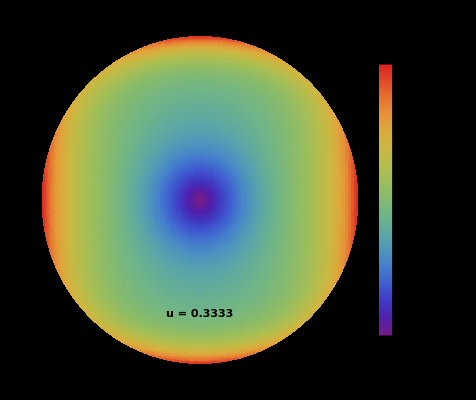

```mathematica
DensityPlot[Denergy[x,y],{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y},0<x^2+y^2<1],ColorFunction->"Rainbow",MeshStyle->Opacity[0.1,Black],PlotLegends->Automatic,Background->Black,Frame->False,Epilog->Text[Style["u = 0.3333",Large,Bold],{0,-0.7}],PlotPoints->100]
```

```mathematica
Denergy[x_,y_]:=
DEnergy[x,y]/.{R->1,n->0.5,u->0.25,Ka->0.01,κ->8π}
```

```mathematica
Denergy[x,y]
```

-((0.0838406 √(x^2+y^2) (-9.×10^-6 (0.36+x^2+y^2) (-1+√(x^2+y^2)) (1+√(x^2+y^2))+1.81131 (0.1296+1.8 (x^2+y^2)+6 (x^2+y^2)^2) AppellF1[3/2,-0.333333,0.333333,5/2,x^2+y^2,-5.55556 (x^2+y^2)]))/((0.36+2 (x^2+y^2))^2 (-3 (3.36-x^2-y^2) (0.36+x^2+y^2)+1.81131 (x^2+y^2) (0.36+2 (x^2+y^2)) AppellF1[3/2,-0.333333,0.333333,5/2,x^2+y^2,-5.55556 (x^2+y^2)])))

```mathematica
Denergy[x_,y_]:=-((0.0838405503787663 √(x^2+y^2) (-9.000000000000002*^-6 (0.3600000000000001+x^2+y^2) (-1+√(x^2+y^2)) (1+√(x^2+y^2))+1.8113081561105093 (0.12960000000000008+1.8000000000000005 (x^2+y^2)+6 (x^2+y^2)^2) AppellF1[3/2,-0.33333333333333337,0.3333333333333333,5/2,x^2+y^2,-5.5555555555555545 (x^2+y^2)]))/((0.3600000000000001+2 (x^2+y^2))^2 (-3 (3.3600000000000003-x^2-y^2) (0.3600000000000001+x^2+y^2)+1.8113081561105093 (x^2+y^2) (0.3600000000000001+2 (x^2+y^2)) AppellF1[3/2,-0.33333333333333337,0.3333333333333333,5/2,x^2+y^2,-5.5555555555555545 (x^2+y^2)])))
```

```mathematica
Series[AppellF1[3/2,-0.33333333333333337,0.3333333333333333,5/2,x^2+y^2,-5.5555555555555545 (x^2+y^2)],{x,0,1}]
```

AppellF1[3/2,-0.333333,0.333333,5/2,y^2,-5.55556 y^2]

```mathematica
Denergy[x_,y_]:=-((0.0838405503787663 √(x^2+y^2) (-9.000000000000002*^-6 (0.3600000000000001+x^2+y^2) (-1+√(x^2+y^2)) (1+√(x^2+y^2))+1.8113081561105093 (0.12960000000000008+1.8000000000000005 (x^2+y^2)+6 (x^2+y^2)^2) AppellF1[3/2,-0.33333333333333337,0.3333333333333333,5/2,y^2,-5.5555555555555545 y^2]))/((0.3600000000000001+2 (x^2+y^2))^2 (-3 (3.3600000000000003-x^2-y^2) (0.3600000000000001+x^2+y^2)+1.8113081561105093 (x^2+y^2) (0.3600000000000001+2 (x^2+y^2)) AppellF1[3/2,-0.33333333333333337,0.3333333333333333,5/2,y^2,-5.5555555555555545 y^2])))
```

```mathematica
Series[AppellF1[3/2,-0.33333333333333337,0.3333333333333333,5/2,y^2,-5.5555555555555545 y^2],{y,0,4}]
```

1.-1.31111 y^2+3.15638 y^4+O[y]^5

```mathematica
Denergy[x_,y_]:=-((0.0838405503787663 √(x^2+y^2) (-9.000000000000002*^-6 (0.3600000000000001+x^2+y^2) (-1+√(x^2+y^2)) (1+√(x^2+y^2))+1.8113081561105093 (0.12960000000000008+1.8000000000000005 (x^2+y^2)+6 (x^2+y^2)^2) (1.-1.311111111111111 y^2+3.156378600823043 y^4))/((0.3600000000000001+2 (x^2+y^2))^2 (-3 (3.3600000000000003-x^2-y^2) (0.3600000000000001+x^2+y^2)+1.8113081561105093 (x^2+y^2) (0.3600000000000001+2 (x^2+y^2)) (1.-1.311111111111111 y^2+3.156378600823043 y^4)))))
```

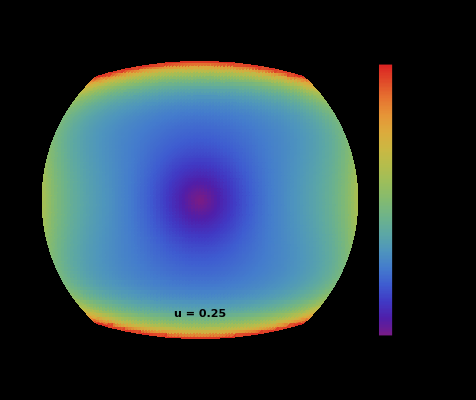

```mathematica
DensityPlot[Denergy[x,y],{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y},0<x^2+y^2<1],ColorFunction->"Rainbow",MeshStyle->Opacity[0.1,Black],PlotLegends->Automatic,Background->Black,Frame->False,Epilog->Text[Style["u = 0.25",Large,Bold],{0,-0.7}],PlotPoints->100]
```

```mathematica
Denergy[x_,y_]:=
DEnergy[x,y]/.{R->1,n->0.5,u->0.20,Ka->0.01,κ->8π}
```

```mathematica
Denergy[x,y]
```

-((0.0908024 √(x^2+y^2) (-9.×10^-6 (1.17893+x^2+y^2) (-1+√(x^2+y^2)) (1+√(x^2+y^2))+1.41063 (1.38988+5.89466 (x^2+y^2)+6 (x^2+y^2)^2) AppellF1[3/2,-0.333333,0.333333,5/2,x^2+y^2,-1.69645 (x^2+y^2)]))/((1.17893+2 (x^2+y^2))^2 (-3 (4.17893-x^2-y^2) (1.17893+x^2+y^2)+1.41063 (x^2+y^2) (1.17893+2 (x^2+y^2)) AppellF1[3/2,-0.333333,0.333333,5/2,x^2+y^2,-1.69645 (x^2+y^2)])))

```mathematica
Denergy[x_,y_]:=-((0.0908024015558501 √(x^2+y^2) (-9.000000000000002*^-6 (1.1789321881345245+x^2+y^2) (-1+√(x^2+y^2)) (1+√(x^2+y^2))+1.4106337344013178 (1.389881104219658+5.8946609406726225 (x^2+y^2)+6 (x^2+y^2)^2) AppellF1[3/2,-0.33333333333333337,0.3333333333333333,5/2,x^2+y^2,-1.6964504151546551 (x^2+y^2)]))/((1.1789321881345245+2 (x^2+y^2))^2 (-3 (4.1789321881345245-x^2-y^2) (1.1789321881345245+x^2+y^2)+1.4106337344013178 (x^2+y^2) (1.1789321881345245+2 (x^2+y^2)) AppellF1[3/2,-0.33333333333333337,0.3333333333333333,5/2,x^2+y^2,-1.6964504151546551 (x^2+y^2)])))
```

```mathematica
Series[AppellF1[3/2,-0.33333333333333337,0.3333333333333333,5/2,x^2+y^2,-1.6964504151546551 (x^2+y^2)],{x,0,1}]
```

AppellF1[3/2,-0.333333,0.333333,5/2,y^2,-1.69645 y^2]

```mathematica
Denergy[x_,y_]:=-((0.0908024015558501 √(x^2+y^2) (-9.000000000000002*^-6 (1.1789321881345245+x^2+y^2) (-1+√(x^2+y^2)) (1+√(x^2+y^2))+1.4106337344013178 (1.389881104219658+5.8946609406726225 (x^2+y^2)+6 (x^2+y^2)^2) AppellF1[3/2,-0.33333333333333337,0.3333333333333333,5/2,y^2,-1.6964504151546551 y^2]))/((1.1789321881345245+2 (x^2+y^2))^2 (-3 (4.1789321881345245-x^2-y^2) (1.1789321881345245+x^2+y^2)+1.4106337344013178 (x^2+y^2) (1.1789321881345245+2 (x^2+y^2)) AppellF1[3/2,-0.33333333333333337,0.3333333333333333,5/2,y^2,-1.6964504151546551 y^2])))
```

```mathematica
Series[AppellF1[3/2,-0.33333333333333337,0.3333333333333333,5/2,y^2,-1.6964504151546551 y^2],{y,0,1}]
```

1.

```mathematica
Denergy[x_,y_]:=-((0.0908024015558501 √(x^2+y^2) (-9.000000000000002*^-6 (1.1789321881345245+x^2+y^2) (-1+√(x^2+y^2)) (1+√(x^2+y^2))+1.4106337344013178 (1.389881104219658+5.8946609406726225 (x^2+y^2)+6 (x^2+y^2)^2) (1.)))/((1.1789321881345245+2 (x^2+y^2))^2 (-3 (4.1789321881345245-x^2-y^2) (1.1789321881345245+x^2+y^2)+1.4106337344013178 (x^2+y^2) (1.1789321881345245+2 (x^2+y^2)) (1.))))*10^2
```

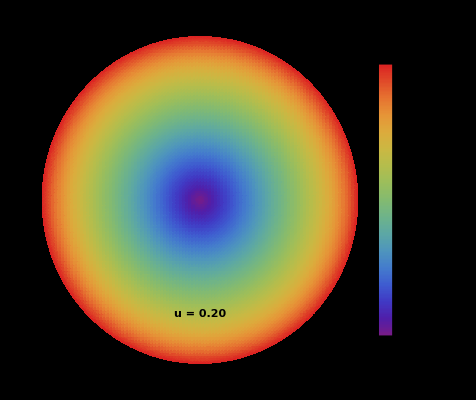

```mathematica
DensityPlot[Denergy[x,y],{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y},0<x^2+y^2<1],ColorFunction->"Rainbow",MeshStyle->Opacity[0.1,Black],PlotLegends->Automatic,Background->Black,Frame->False,Epilog->Text[Style["u = 0.20",Large,Bold],{0,-0.7}],PlotPoints->100]
```

```mathematica
Denergy[x_,y_]:=
DEnergy[x,y]/.{R->1,n->0.5,u->0.22,Ka->0.01,κ->8π}
```

```mathematica
Denergy[x,y]
```

-((0.0886333 √(x^2+y^2) (-9.×10^-6 (0.883987+x^2+y^2) (-1+√(x^2+y^2)) (1+√(x^2+y^2))+1.47878 (0.781434+4.41994 (x^2+y^2)+6 (x^2+y^2)^2) AppellF1[3/2,-0.333333,0.333333,5/2,x^2+y^2,-2.26248 (x^2+y^2)]))/((0.883987+2 (x^2+y^2))^2 (-3 (3.88399-x^2-y^2) (0.883987+x^2+y^2)+1.47878 (x^2+y^2) (0.883987+2 (x^2+y^2)) AppellF1[3/2,-0.333333,0.333333,5/2,x^2+y^2,-2.26248 (x^2+y^2)])))

```mathematica
Denergy[x_,y_]:=-((0.08863330522380237 √(x^2+y^2) (-9.000000000000002*^-6 (0.8839874916296523+x^2+y^2) (-1+√(x^2+y^2)) (1+√(x^2+y^2))+1.4787797669841531 (0.7814338853576845+4.4199374581482616 (x^2+y^2)+6 (x^2+y^2)^2) AppellF1[3/2,-0.33333333333333337,0.3333333333333333,5/2,x^2+y^2,-2.2624754523539146 (x^2+y^2)]))/((0.8839874916296523+2 (x^2+y^2))^2 (-3 (3.8839874916296524-x^2-y^2) (0.8839874916296523+x^2+y^2)+1.4787797669841531 (x^2+y^2) (0.8839874916296523+2 (x^2+y^2)) AppellF1[3/2,-0.33333333333333337,0.3333333333333333,5/2,x^2+y^2,-2.2624754523539146 (x^2+y^2)])))
```

```mathematica
Series[AppellF1[3/2,-0.33333333333333337,0.3333333333333333,5/2,x^2+y^2,-2.2624754523539146 (x^2+y^2)],{x,0,1}]
```

AppellF1[3/2,-0.333333,0.333333,5/2,y^2,-2.26248 y^2]

```mathematica
Series[AppellF1[3/2,-0.33333333333333337,0.3333333333333333,5/2,y^2,-2.2624754523539146 y^2],{y,0,4}]
```

1.-0.652495 y^2+0.547622 y^4+O[y]^5

```mathematica
Denergy[x_,y_]:=-((0.08301786806422434 √(x^2+y^2) (-9.000000000000002*^-6 (0.2839521630550498+x^2+y^2) (-1+√(x^2+y^2)) (1+√(x^2+y^2))+1.9307074795172 (0.08062883090364158+1.4197608152752488 (x^2+y^2)+6 (x^2+y^2)^2) (1.-0.6524950904707829 y^2+0.5476221808267625 y^4)))/((0.2839521630550498+2 (x^2+y^2))^2 (-3 (3.2839521630550497-x^2-y^2) (0.2839521630550498+x^2+y^2)+1.9307074795172 (x^2+y^2) (0.2839521630550498+2 (x^2+y^2)) (1.-0.6524950904707829 y^2+0.5476221808267625 y^4))))
```

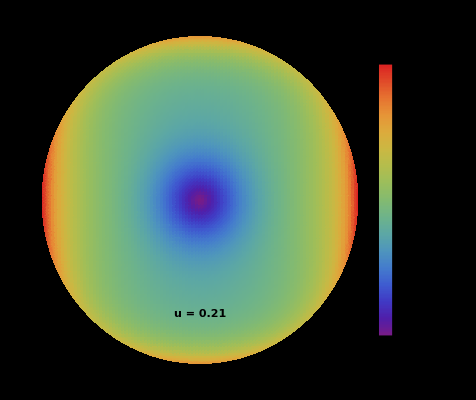

```mathematica
DensityPlot[Denergy[x,y],{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y},0<x^2+y^2<1],ColorFunction->"Rainbow",MeshStyle->Opacity[0.1,Black],PlotLegends->Automatic,Background->Black,Frame->False,Epilog->Text[Style["u = 0.21",Large,Bold],{0,-0.7}],PlotPoints->100]
```